### Dynamical Systems TIF155/FIM770 Konstantinos Zakkas Problem Set 1

### 1.4 Two-dimensional linear system a)

```mathematica
M = {{σ+1, 3},{-2, σ-1}}
X[t_]={x[t],y[t]}
dynSystem = X'[t] == M.X[t]
```

{{1+σ,3},{-2,-1+σ}}

{x[t],y[t]}

{x'[t],y'[t]}=={(1+σ) x[t]+3 y[t],-2 x[t]+(-1+σ) y[t]}

```mathematica
Eigenvalues[M]
```

{-ⅈ √5+σ,ⅈ √5+σ}

### b)

```mathematica
sol=DSolve[dynSystem,{x,y},t]
```

{{x→Function[{t},(3 ⅇ^(t σ) C[2] Sin[√5 t])/(√5)+1/5 ⅇ^(t σ) C[1] (5 Cos[√5 t]+√5 Sin[√5 t])],y→Function[{t},-(2 ⅇ^(t σ) C[1] Sin[√5 t])/(√5)+1/5 ⅇ^(t σ) C[2] (5 Cos[√5 t]-√5 Sin[√5 t])]}}

```mathematica
X[t_,x0_,y0_,σ_]={x[t],y[t]}/.sol/.{C[1]->u, C[2]->v}
```

{{(3 ⅇ^(t σ) v Sin[√5 t])/(√5)+1/5 ⅇ^(t σ) u (5 Cos[√5 t]+√5 Sin[√5 t]),-(2 ⅇ^(t σ) u Sin[√5 t])/(√5)+1/5 ⅇ^(t σ) v (5 Cos[√5 t]-√5 Sin[√5 t])}}

### c)

```mathematica
p1=ParametricPlot[X[t,1,1,-0.1],{t,0,10}, AxesLabel->{"x","y"}, PlotLabel->"σ=-0.1"]/.Line->Arrow;
p2=ParametricPlot[X[t,1,1,0],{t,0,10},AxesLabel->{"x","y"}, PlotLabel->"σ=0"]/.Line->Arrow;
p3=ParametricPlot[X[t,1,1,0.1],{t,0,10},AxesLabel->{"x","y"}, PlotLabel->"σ=0.1"]/.Line->Arrow;
plot = {p1,p2,p3};
Show[GraphicsRow[plot]]
```

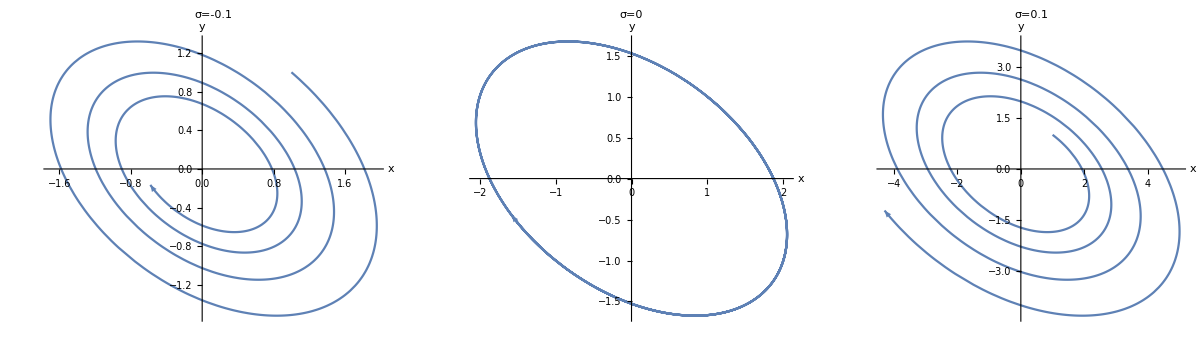

### d)

```mathematica
Solve [X[0,u,v,0]== X[t,u,v,0],t]
```

{{t→ConditionalExpression[(2 π C[1])/(√5), C[1]∈ℤ]}}

```mathematica
X[t_,x0_,y0_] = X[t,u,v,0] //Simplify
```

{{u Cos[√5 t]+((u+3 v) Sin[√5 t])/(√5),v Cos[√5 t]-((2 u+v) Sin[√5 t])/(√5)}}

```mathematica
L[t_] = X[t,x0,y0][[1]][[1]]^2  + X[t,x0,y0][[1]][[2]]^2
```

(v Cos[√5 t]-((2 u+v) Sin[√5 t])/(√5))^2+(u Cos[√5 t]+((u+3 v) Sin[√5 t])/(√5))^2

```mathematica
L[t_]=L[t]//Simplify
```

(v Cos[√5 t]-((2 u+v) Sin[√5 t])/(√5))^2+(u Cos[√5 t]+((u+3 v) Sin[√5 t])/(√5))^2

```mathematica
dL[t_] = D[L[t],t]
```

2 (-((2 u+v) Cos[√5 t])-√5 v Sin[√5 t]) (v Cos[√5 t]-((2 u+v) Sin[√5 t])/(√5))+2 ((u+3 v) Cos[√5 t]-√5 u Sin[√5 t]) (u Cos[√5 t]+((u+3 v) Sin[√5 t])/(√5))

```mathematica
dL[t_]=dL[t]//Simplify
```

2 (u^2+u v-v^2) Cos[2 √5 t]+√5 v (2 u+v) Sin[2 √5 t]

```mathematica
tVal =Solve[dL[t]==0,t]
```

{{t→ConditionalExpression[1/(2 √5)(ArcTan[-(√5 v (2 u+v))/(√(4 u^4+8 u^3 v+16 u^2 v^2+12 u v^3+9 v^4)),1/(2 u+v)2 ((2 u^3)/(√((2 u^2+2 u v+3 v^2)^2))+(3 u^2 v)/(√((2 u^2+2 u v+3 v^2)^2))-(u v^2)/(√((2 u^2+2 u v+3 v^2)^2))-v^3/(√((2 u^2+2 u v+3 v^2)^2)))]+2 π C[1]), C[1]∈ℤ]},{t→ConditionalExpression[1/(2 √5)(ArcTan[(√5 v (2 u+v))/(√(4 u^4+8 u^3 v+16 u^2 v^2+12 u v^3+9 v^4)),1/(2 u+v)2 (-(2 u^3)/(√((2 u^2+2 u v+3 v^2)^2))-(3 u^2 v)/(√((2 u^2+2 u v+3 v^2)^2))+(u v^2)/(√((2 u^2+2 u v+3 v^2)^2))+v^3/(√((2 u^2+2 u v+3 v^2)^2)))]+2 π C[1]), C[1]∈ℤ]}}

```mathematica
tVal=tVal//Simplify
```

{{t→ConditionalExpression[(ArcTan[-(√5 v (2 u+v))/(√((2 u^2+2 u v+3 v^2)^2)),(2 (u^2+u v-v^2))/(√((2 u^2+2 u v+3 v^2)^2))]+2 π C[1])/(2 √5), C[1]∈ℤ]},{t→ConditionalExpression[(ArcTan[(√5 v (2 u+v))/(√((2 u^2+2 u v+3 v^2)^2)),-(2 (u^2+u v-v^2))/(√((2 u^2+2 u v+3 v^2)^2))]+2 π C[1])/(2 √5), C[1]∈ℤ]}}

```mathematica
t1=t/.tVal[[1]]
```

ConditionalExpression[(ArcTan[-(√5 v (2 u+v))/(√((2 u^2+2 u v+3 v^2)^2)),(2 (u^2+u v-v^2))/(√((2 u^2+2 u v+3 v^2)^2))]+2 π C[1])/(2 √5), C[1]∈ℤ]

```mathematica
t2=t/.tVal[[2]]
```

ConditionalExpression[(ArcTan[(√5 v (2 u+v))/(√((2 u^2+2 u v+3 v^2)^2)),-(2 (u^2+u v-v^2))/(√((2 u^2+2 u v+3 v^2)^2))]+2 π C[1])/(2 √5), C[1]∈ℤ]

```mathematica
R = Sqrt[L[t1]/L[t2]]
```

ConditionalExpression[√(((v Cos[1/2 (ArcTan[-(√5 v (2 u+v))/(√((2 u^2+2 u v+3 v^2)^2)),(2 (u^2+u v-v^2))/(√((2 u^2+2 u v+3 v^2)^2))]+2 π C[1])]-1/(√5)(2 u+v) Sin[1/2 (ArcTan[-(√5 v (2 u+v))/(√((2 u^2+2 u v+3 v^2)^2)),(2 (u^2+u v-v^2))/(√((2 u^2+2 u v+3 v^2)^2))]+2 π C[1])])^2+(u Cos[1/2 (ArcTan[-(√5 v (2 u+v))/(√((2 u^2+2 u v+3 v^2)^2)),(2 (u^2+u v-v^2))/(√((2 u^2+2 u v+3 v^2)^2))]+2 π C[1])]+1/(√5)(u+3 v) Sin[1/2 (ArcTan[-(√5 v (2 u+v))/(√((2 u^2+2 u v+3 v^2)^2)),(2 (u^2+u v-v^2))/(√((2 u^2+2 u v+3 v^2)^2))]+2 π C[1])])^2)/((v Cos[1/2 (ArcTan[(√5 v (2 u+v))/(√((2 u^2+2 u v+3 v^2)^2)),-(2 (u^2+u v-v^2))/(√((2 u^2+2 u v+3 v^2)^2))]+2 π C[1])]-1/(√5)(2 u+v) Sin[1/2 (ArcTan[(√5 v (2 u+v))/(√((2 u^2+2 u v+3 v^2)^2)),-(2 (u^2+u v-v^2))/(√((2 u^2+2 u v+3 v^2)^2))]+2 π C[1])])^2+(u Cos[1/2 (ArcTan[(√5 v (2 u+v))/(√((2 u^2+2 u v+3 v^2)^2)),-(2 (u^2+u v-v^2))/(√((2 u^2+2 u v+3 v^2)^2))]+2 π C[1])]+1/(√5)(u+3 v) Sin[1/2 (ArcTan[(√5 v (2 u+v))/(√((2 u^2+2 u v+3 v^2)^2)),-(2 (u^2+u v-v^2))/(√((2 u^2+2 u v+3 v^2)^2))]+2 π C[1])])^2)), C[1]∈ℤ]

```mathematica
R = Simplify[R/.C[1]->0]
```

√(-(2 √5 u^2+2 √5 u v+3 √5 v^2+5 √((2 u^2+2 u v+3 v^2)^2))/(2 √5 u^2+2 √5 u v+3 √5 v^2-5 √((2 u^2+2 u v+3 v^2)^2)))

```mathematica
R=Simplify[R,{Element[u,Reals],Element[v,Reals]}]
```

√(1/2 (3+√5))

```mathematica
N[R]
```

1.61803

```mathematica
u=.;
v=.;
direction = X[t1/.C[1]->0,u,v]//Simplify
u=1;
v=1;
dir = Normalize[direction[[1]]] //Simplify//TrigReduce//Expand//TrigExpand//PowerExpand//Simplify
N[dir]
```

{{u Cos[1/2 ArcTan[-(√5 v (2 u+v))/(√((2 u^2+2 u v+3 v^2)^2)),(2 (u^2+u v-v^2))/(√((2 u^2+2 u v+3 v^2)^2))]]+((u+3 v) Sin[1/2 ArcTan[-(√5 v (2 u+v))/(√((2 u^2+2 u v+3 v^2)^2)),(2 (u^2+u v-v^2))/(√((2 u^2+2 u v+3 v^2)^2))]])/(√5),v Cos[1/2 ArcTan[-(√5 v (2 u+v))/(√((2 u^2+2 u v+3 v^2)^2)),(2 (u^2+u v-v^2))/(√((2 u^2+2 u v+3 v^2)^2))]]-((2 u+v) Sin[1/2 ArcTan[-(√5 v (2 u+v))/(√((2 u^2+2 u v+3 v^2)^2)),(2 (u^2+u v-v^2))/(√((2 u^2+2 u v+3 v^2)^2))]])/(√5)}}

{-1/10 (-5+√5) √(5+2 √5),-(3+√5)/(√(50+22 √5))}

{0.850651,-0.525731}